#### Assignment - 1 : Solving Problems on Multivariate and Vector Calculus with its Real - life Applications Answer to the question no - 01 (a) (i)[Butterfly]

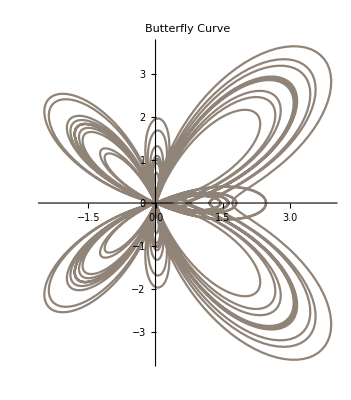

```mathematica
PolarPlot[ E^Cos[θ]-2 Cos[4 θ] + Sin[θ/12]^5, {θ, 0, 24 π},PlotLabel->"Butterfly Curve", ColorFunction->"Rainbow"]
```

#### (ii)[Tricuspoid]

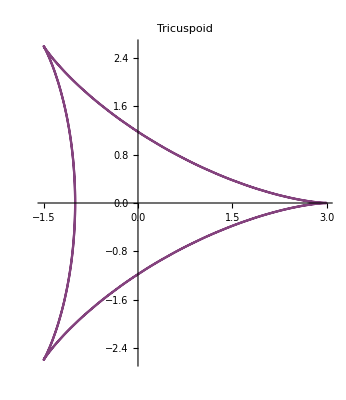

```mathematica
ParametricPlot[{2Cos[t]+Cos[2t],2Sin[t]-Sin[2t]},{t,0,4π},PlotLabel->"Tricuspoid", ColorFunction->"Rainbow"]
```

#### (iii)[Cornu spiral]

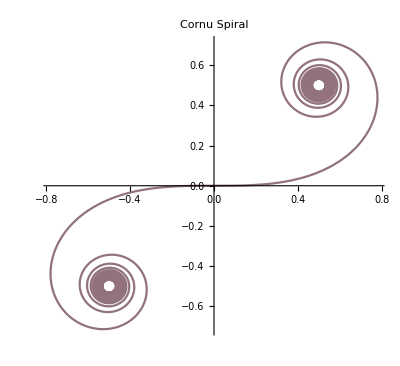

```mathematica
ParametricPlot[{∫_0^t Cos[(π*u^2)/2]ⅆu,∫_0^t Sin[(π*u^2)/2]ⅆu},{t,-10,10},PlotLabel->"Cornu Spiral", ColorFunction->"Rainbow"]
```

#### (iv)[Circular Helix]

```mathematica
a=1;c=1/3;
ParametricPlot3D[{a*Cos[t],a*Sin[t],c*t},{t,π/3,8π},PlotLabel->"Circular Helix", ColorFunction->Hue]
```

-Graphics3D-

#### (b) (i)

```mathematica
p1=Plot3D[{x^2+y^2,12-y},{x,-5,5},{y,-5,5}];
p2=ParametricPlot3D[{{Sqrt[(12-t)-t^2],t,12-t},{-Sqrt[(12-t)-t^2],t,12-t}},{t,-2π,2π},PlotStyle->Red];
Show[p1,p2,ViewPoint->{1.3, -2.4, 2.},AxesLabel->{"x","y","z"}]
Show[p1,p2,ViewPoint->Top,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

-Graphics3D-

#### (ii)

```mathematica
p1=ContourPlot3D[{9x^2+y^2+9z^2==81,y==x^2},{x,-5,5},{y,-5,5},{z,0,5}];
p2=ParametricPlot3D[{{t,t^2,Sqrt[81-9t^2-t^4]/3},{t,t^2,(-Sqrt[81-9t^2-t^4])/3}},{t,-2Pi,2Pi},PlotStyle->Red];
Show[p1,p2,ViewPoint->{1.3, -2.4, 2.},AxesLabel->{"x","y","z"}]
Show[p1,p2,ViewPoint->{0, 1, 2},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

-Graphics3D-

```mathematica
OR
```

```mathematica
p1=Plot3D[{-Sqrt[81-9 x^2-9 z^2],Sqrt[81-9 x^2-9 z^2],x^2},{x,-5,5},{z,0,5},PlotStyle->{Green,Green,Gray}];p2=ParametricPlot3D[{{t,Sqrt[81-9t^2-t^4]/3,t^2},{t,(-Sqrt[81-9t^2-t^4])/3,t^2}},{t,-2Pi,2Pi},PlotStyle->Red];
Show[p1,p2,ViewPoint->{1.3, -2.4, 2.},AxesLabel->{"x","z","y"}]
Show[p1,p2,ViewPoint->Front,AxesLabel->{"x","z","y"}]
```

-Graphics3D-

-Graphics3D-

### (iii)

```mathematica
p1=Plot3D[x^2+y^2,{x,-5,5},{y,-5,5}];
p2=ParametricPlot3D[{t Sin[t],t Cos[t],t^2},{t,-2Pi,2Pi},PlotStyle->{Blue,Thick}];
Show[p1,p2,ViewPoint->{1.3, -2.4, 2.},AxesLabel->{"x","y","z"}]
Show[p1,p2,ViewPoint->Front,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

-Graphics3D-

#### (b) (i)[contour plot]

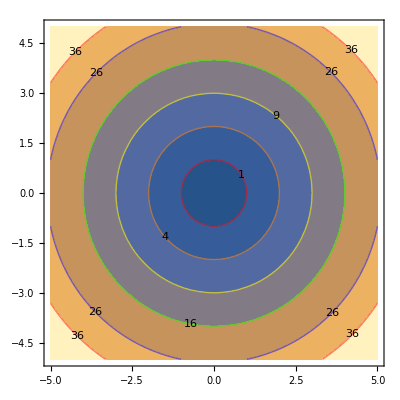

```mathematica
ContourPlot[x^2+y^2,{x,-5,5},{y,-5,5},Contours->{1,4,9,16,26,36},AspectRatio->Automatic,ContourStyle->{Red, Orange, Yellow, Green, Blue},ContourLabels->True]
```

### (ii)[contour plot 3D]

```mathematica
ContourPlot3D[z^2-x^2-y^2,{x,-5,5},{y,-5,5},{z,-5,5},Contours->{1,4,9,16,26,36},AspectRatio->Automatic,ContourStyle->{Brown, Orange, Yellow, Green, Blue}]
```

-Graphics3D-

### Answer to the question no - 2 (a) (i)

-Graphics3D-

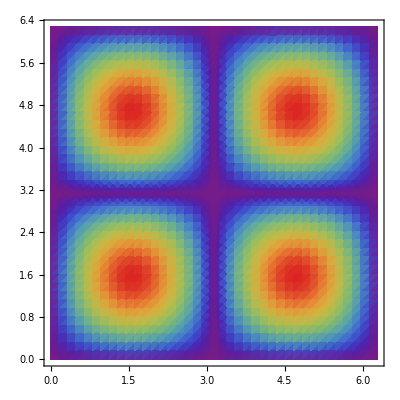

```mathematica
Plot3D[Abs[Sin[x]*Sin[y]],{x,0,2π},{y,0,2π},Axes->True,PlotPoints->26,ColorFunction->"TemperatureMap",PlotStyle->Automatic]
DensityPlot[Abs[Sin[x]*Sin[y]],{x,0,2Pi},{y,0,2Pi},Axes->True,PlotPoints->40,ColorFunction->"Rainbow"]
```

### (ii)

-Graphics3D-

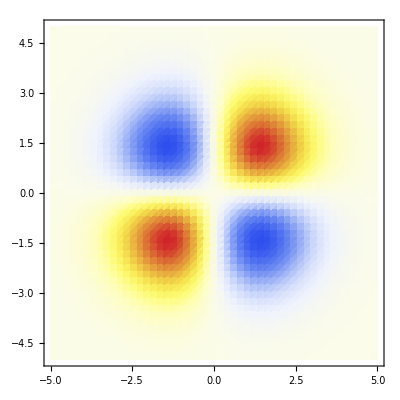

```mathematica
Plot3D[x *y *ⅇ^(-1/4(x^2+y^2)),{x,-5,5},{y,-5,5},Axes->True,PlotPoints->40,ColorFunction->"Rainbow",PlotStyle->Automatic]
DensityPlot[x*y*ⅇ^(-1/4(x^2+y^2)),{x,-5,5},{y,-5,5},Axes->True,PlotPoints->50,ColorFunction->"TemperatureMap"]
```

### (b) (i)

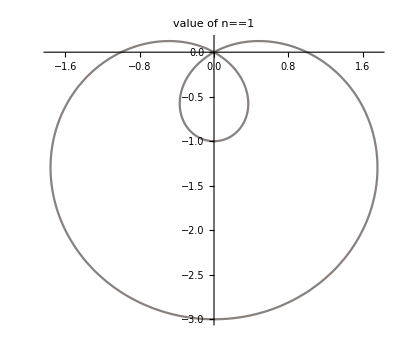
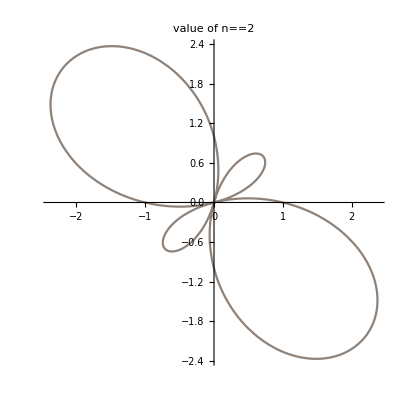
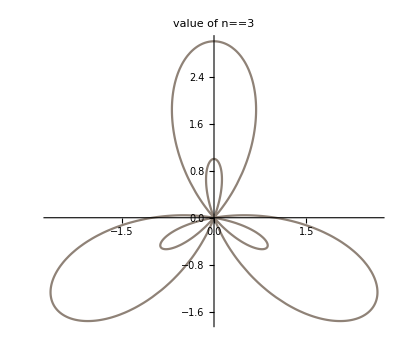
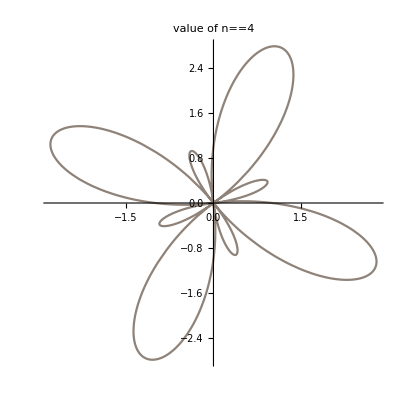
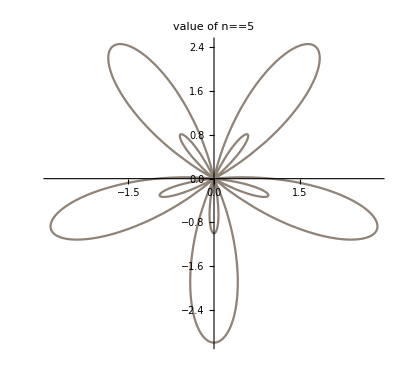
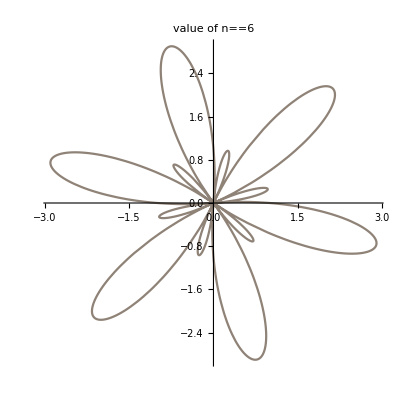
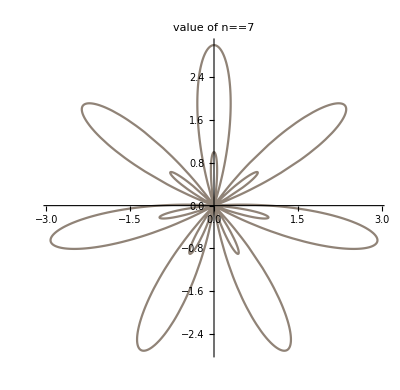
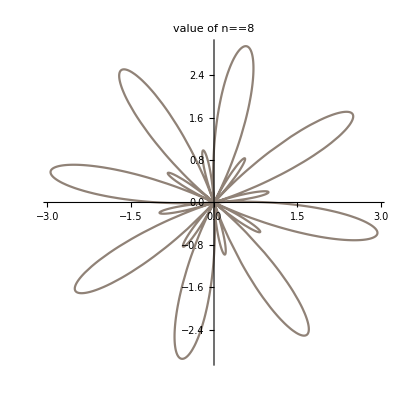

```mathematica
Table[PolarPlot[1-2Sin[n*θ],{θ,0,2π},ColorFunction->"Rainbow",PlotLabel->TraditionalForm[HoldForm["value of n"]==n]],{n,1,10}]
```

## Behaviour : “for n being an odd number there are n nested loops and n outer loops otherwise n being an even number there are 2n outer loops”

### (ii)

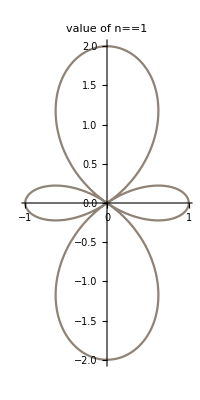
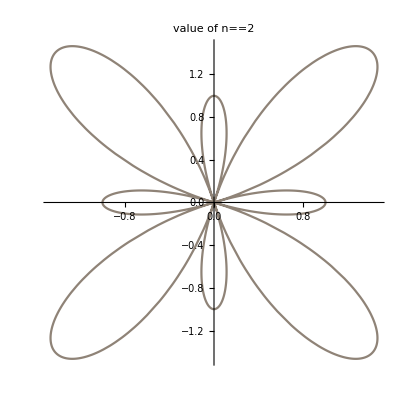
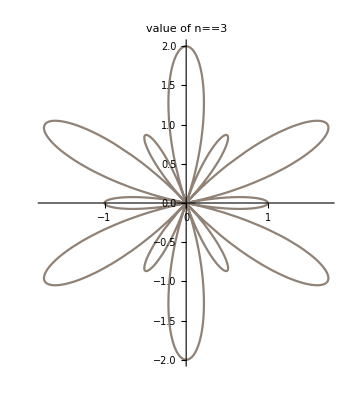
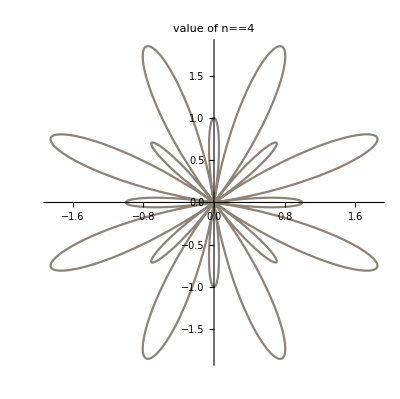
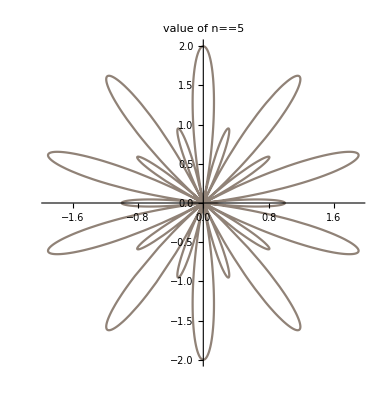
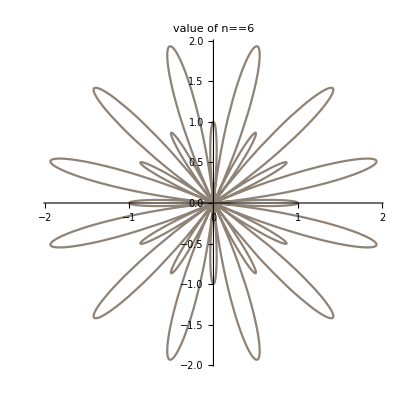
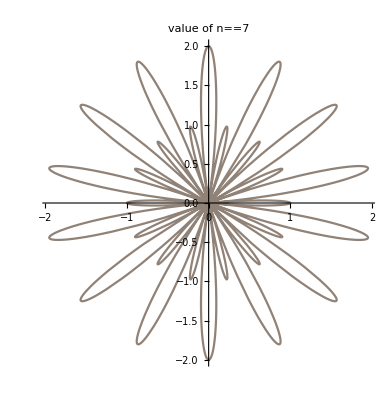
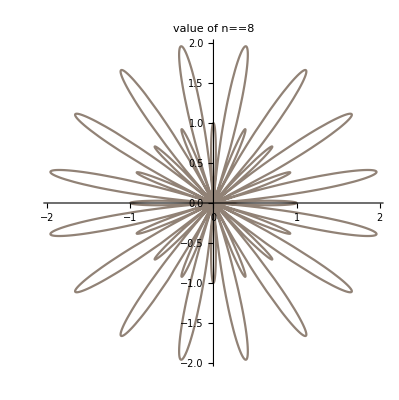

```mathematica
Table[PolarPlot[2-3(Cos[n*θ])^2,{θ,0,2π},ColorFunction->"Rainbow",PlotLabel->TraditionalForm[HoldForm["value of n"]==n]],{n,1,10}]
```

```mathematica
Behaviour : 
"for n being an even or an odd number there are 4n number of loops"
```

```mathematica
Answer to the question no - 3
(a)
```

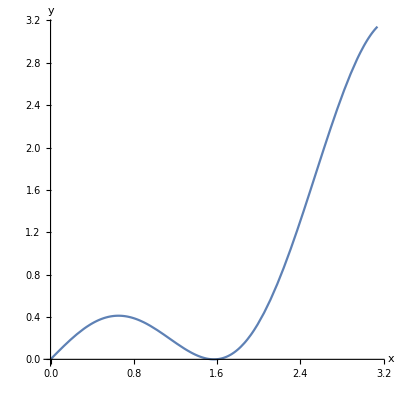

Revolution about x axis :

-Graphics3D-

Revolution about y axis :

-Graphics3D-

```mathematica
Plot[x(Cos[x])^2,{x,0,π},AspectRatio->1,AxesLabel->{"x","y"},PlotLegends->"xcos^2x"]
Print["Revolution about x axis :"]
RevolutionPlot3D[x (Cos[x]^2),{x,0,Pi},RevolutionAxis->{1, 0, 0},AspectRatio->1,PlotLabel->"about x-axis",AxesLabel->{"x","y","z"},ColorFunction->"Rainbow"]
Print["Revolution about y axis :"]
RevolutionPlot3D[x(Cos[x])^2,{x,0,π},RevolutionAxis->{0, 0, 1},AspectRatio->1,PlotLabel->"about y-axis",AxesLabel->{"x","z","y"},ColorFunction->"Rainbow"]
```

### volume about x-axis(disk method) :

```mathematica
∫_0^π π*(x*Cos[x]^2)^2 ⅆx
```

1/64 π^2 (17+8 π^2)

### volume about y-axis (cylindrical shell method):

```mathematica
∫_0^π 2π*x(x*Cos[x]^2)ⅆx
```

1/6 π^2 (3+2 π^2)

```mathematica
(b)
```

#### equation of tangent plane and normal line :

```mathematica
f[x_,y_,z_]:=z-ⅇ^x Sin[π*y]
p={x,y,z};q={0,1,0};
n=Grad[f[x,y,z],{x,y,z}]/.x->0/.y->1/.z->0;
Print["Equation of Tangent Plane :"]
n.(p-q)==0
Print["Equation of Normal Line :"]
p==q+n*t
```

Equation of Tangent Plane :

π (-1+y)+z==0

Equation of Normal Line :

{x,y,z}=={0,1+π t,t}

#### plotting graphically :

```mathematica
p1=ParametricPlot3D[{0,1+π t,t},{t,-10,10},PlotStyle->Red,PlotLegends->{"Normal line"}];
p2=ContourPlot3D[{f[x,y,z]==0,π (-1+y)+z==0},{x,-6,6},{y,-6,6},{z,-6,6},PlotLegends->{"f(x,y,z)","tangent plane"}];
Show[p2,p1]
```

-Graphics3D-

```mathematica
Answer to the question no - 4
(a)
```

Gradient of T(x,y) at the point (-1,3/2) :

{-9,3}

Plotting Gradient of T(x,y) :

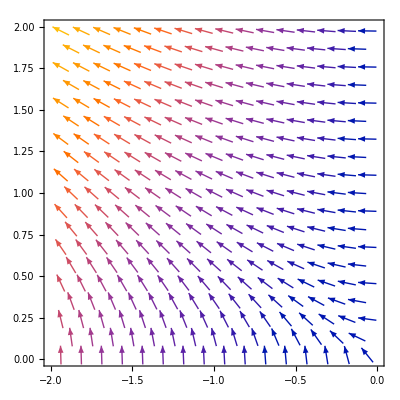

Directional Derivative of T(x,y) at (-1,3/2) in the direction of (-1,-1/2) :

3 √5

Plotting Directional Derivative of T(x,y) in the direction of (-1,-1/2) :

-Graphics3D-

```mathematica
T[x_,y_] := 3 x^2 y;u={-1,-1/2};
Print["Gradient of T(x,y) at the point (-1,3/2) :"]
Grad[T[x,y],{x,y}]/.x->-1/.y->3/2
Print["Plotting Gradient of T(x,y) :"]
VectorPlot[{6 x y,3 x^2},{x,-2,0},{y,0,2}]
Print["Directional Derivative of T(x,y) at (-1,3/2) in the direction of (-1,-1/2) :"]
{-9,3}.(u/Norm[u])
Print["Plotting Directional Derivative of T(x,y) in the direction of (-1,-1/2) :"]
Plot3D[-(3 x^2)/(√5)-(12 x y)/(√5),{x,-2,0},{y,0,2}]
```

```mathematica
Answer to the question no - 4
(b)(i)
```

{-1,-1} have a relative maximum

{0,0} have a saddle point

{1,1} have a relative maximum

-Graphics3D-

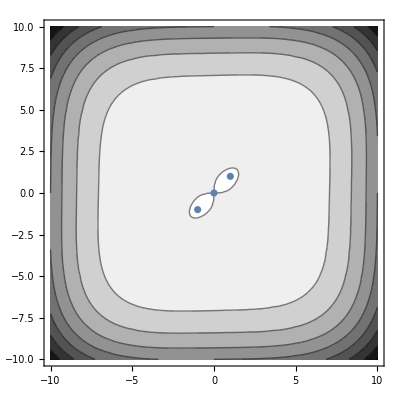

```mathematica
f[x_,y_]:=4x y-x^4-y^4;
p1=Plot3D[f[x,y],{x,-5,5},{y,-5,5},PlotStyle->Gray];
{e1,e2}=Grad[f[x,y],{x,y}];
points={x,y}/.Solve[{e1==0,e2==0},{x,y},Reals];
DD=D[f[x,y],x,x]D[f[x,y],y,y]-(D[f[x,y],x,y])^2;
Do[{
If[DD>0/.x->points[[i]][[1]]/.y->points[[i]][[2]],If[D[f[x,y],x,x]>=0/.x->points[[i]][[1]]/.y->points[[i]][[2]],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Blue,PlotLegends->{"Minimum at "StandardForm[points[[i]]],Blue}];Print[points[[i]]," have a relative minimum"],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Red,PlotLegends->{"Maximum at "StandardForm[points[[i]]],Red}];Print[points[[i]]," have a relative maximum"]]],
If[DD<0/.x->points[[i]][[1]]/.y->points[[i]][[2]],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Green,PlotLegends->{"Saddle point at"StandardForm[points[[i]]],Green}];Print[points[[i]]," have a saddle point"]]
},{i,1,Length[points]}]
Show[p1,Show[Table[Subscript[p, i],{i,1,Length[points]}]]]
Show[ContourPlot[f[x,y],{x,-10,10},{y,-10,10},ColorFunction->GrayLevel],ListPlot[points]]
```

```mathematica
(b)(ii)
```

{0,0} have a saddle point

{2/5 (Root-2.04Root[-625-1000 #1^2+16 #1^8&,1]-2.0391492949091967)^3,Root-2.04Root[-625-1000 #1^2+16 #1^8&,1]-2.0391492949091967} have a relative minimum

{2/5 (Root2.04Root[-625-1000 #1^2+16 #1^8&,2]2.0391492949091967)^3,Root2.04Root[-625-1000 #1^2+16 #1^8&,2]2.0391492949091967} have a relative minimum

-Graphics3D-

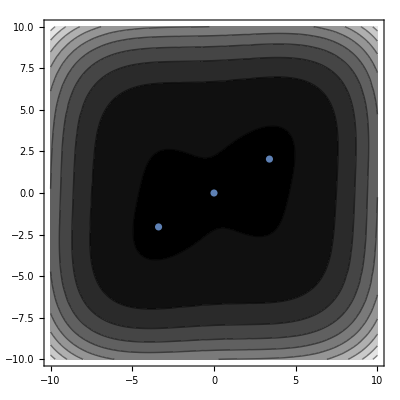

```mathematica
f[x_,y_]:= x^4+y^4-20 x^2-10x y - 25;
p1=Plot3D[f[x,y],{x,-5,5},{y,-5,5},PlotStyle->Gray];
{e1,e2}=Grad[f[x,y],{x,y}];
points={x,y}/.Solve[{e1==0,e2==0},{x,y},Reals];
DD=D[f[x,y],x,x]D[f[x,y],y,y]-(D[f[x,y],x,y])^2;
Do[{
If[DD>0/.x->points[[i]][[1]]/.y->points[[i]][[2]],If[D[f[x,y],x,x]>=0/.x->points[[i]][[1]]/.y->points[[i]][[2]],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Blue,PlotLegends->{"Minimum at "StandardForm[points[[i]]],Blue}];Print[points[[i]]," have a relative minimum"],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Red,PlotLegends->{"Maximum at "StandardForm[points[[i]]],Red}];Print[points[[i]]," have a relative maximum"]]],
If[DD<0/.x->points[[i]][[1]]/.y->points[[i]][[2]],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Green,PlotLegends->{"Saddle point at"StandardForm[points[[i]]],Green}];Print[points[[i]]," have a saddle point"]]
},{i,1,Length[points]}]
Show[p1,Show[Table[Subscript[p, i],{i,1,Length[points]}]]]
Show[ContourPlot[f[x,y],{x,-10,10},{y,-10,10},ColorFunction->GrayLevel],ListPlot[points]]
```

```mathematica
(b)(iii)
```

{1,0} have a relative maximum

-Graphics3D-

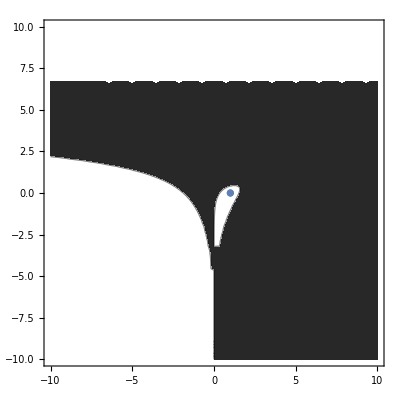

```mathematica
f[x_,y_]:=3 x E^y-x^3-E^(3y);
p1=Plot3D[f[x,y],{x,-5,5},{y,-5,5},PlotStyle->Gray];
{e1,e2}=Grad[f[x,y],{x,y}];
points={x,y}/.Solve[{e1==0,e2==0},{x,y},Reals];
DD=D[f[x,y],x,x]D[f[x,y],y,y]-(D[f[x,y],x,y])^2;
Do[{
If[DD>0/.x->points[[i]][[1]]/.y->points[[i]][[2]],If[D[f[x,y],x,x]>=0/.x->points[[i]][[1]]/.y->points[[i]][[2]],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Blue,PlotLegends->{"Minimum at "StandardForm[points[[i]]],Blue}];Print[points[[i]]," have a relative minimum"],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Red,PlotLegends->{"Maximum at "StandardForm[points[[i]]],Red}];Print[points[[i]]," have a relative maximum"]]],
If[DD<0/.x->points[[i]][[1]]/.y->points[[i]][[2]],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Green,PlotLegends->{"Saddle point at"StandardForm[points[[i]]],Green}];Print[points[[i]]," have a saddle point"]]
},{i,1,Length[points]}]
Show[p1,Show[Table[Subscript[p, i],{i,1,Length[points]}]]]
Show[ContourPlot[f[x,y],{x,-10,10},{y,-10,10},ColorFunction->GrayLevel],ListPlot[points]]
```

```mathematica
(b)(iv)
```

{-1,-1} have a relative maximum

{1,-1} have a saddle point

{-1,1} have a saddle point

{1,1} have a relative minimum

-Graphics3D-

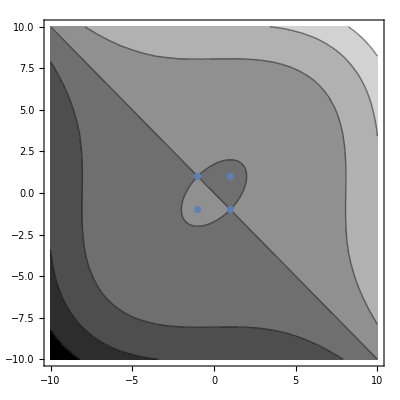

```mathematica
f[x_,y_]:=x^3+y^3-3x-3y;
p1=Plot3D[f[x,y],{x,-5,5},{y,-5,5},PlotStyle->Gray];
{e1,e2}=Grad[f[x,y],{x,y}];
points={x,y}/.Solve[{e1==0,e2==0},{x,y},Reals];
DD=D[f[x,y],x,x]D[f[x,y],y,y]-(D[f[x,y],x,y])^2;
Do[{
If[DD>0/.x->points[[i]][[1]]/.y->points[[i]][[2]],If[D[f[x,y],x,x]>=0/.x->points[[i]][[1]]/.y->points[[i]][[2]],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Blue,PlotLegends->{"Minimum at "StandardForm[points[[i]]],Blue}];Print[points[[i]]," have a relative minimum"],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Red,PlotLegends->{"Maximum at "StandardForm[points[[i]]],Red}];Print[points[[i]]," have a relative maximum"]]],
If[DD<0/.x->points[[i]][[1]]/.y->points[[i]][[2]],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Green,PlotLegends->{"Saddle point at"StandardForm[points[[i]]],Green}];Print[points[[i]]," have a saddle point"]]
},{i,1,Length[points]}]
Show[p1,Show[Table[Subscript[p, i],{i,1,Length[points]}]]]
Show[ContourPlot[f[x,y],{x,-10,10},{y,-10,10},ColorFunction->GrayLevel],ListPlot[points]]
```

```mathematica
(b)(v)
```

{-1,0} have a relative maximum

{1,0} have a relative maximum

-Graphics3D-

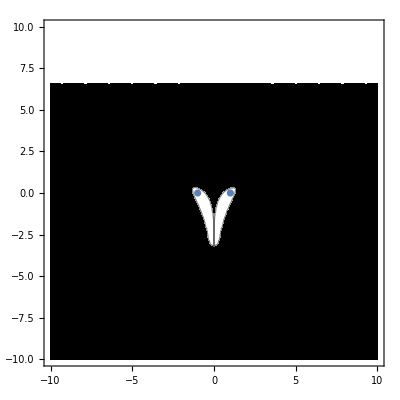

```mathematica
f[x_,y_]:=4 x^2 E^y-2 x^4-E^(4 y);
p1=Plot3D[f[x,y],{x,-5,5},{y,-5,5},PlotStyle->Gray];
{e1,e2}=Grad[f[x,y],{x,y}];
points={x,y}/.Solve[{e1==0,e2==0},{x,y},Reals];
DD=D[f[x,y],x,x]D[f[x,y],y,y]-(D[f[x,y],x,y])^2;
Do[{
If[DD>0/.x->points[[i]][[1]]/.y->points[[i]][[2]],If[D[f[x,y],x,x]>=0/.x->points[[i]][[1]]/.y->points[[i]][[2]],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Blue,PlotLegends->{"Minimum at "StandardForm[points[[i]]],Blue}];Print[points[[i]]," have a relative minimum"],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Red,PlotLegends->{"Maximum at "StandardForm[points[[i]]],Red}];Print[points[[i]]," have a relative maximum"]]],
If[DD<0/.x->points[[i]][[1]]/.y->points[[i]][[2]],Subscript[p, i]=ListPointPlot3D[{{points[[i]][[1]],points[[i]][[2]],f[points[[i]][[1]],points[[i]][[2]]]}},PlotStyle->Green,PlotLegends->{"Saddle point at"StandardForm[points[[i]]],Green}];Print[points[[i]]," have a saddle point"]]
},{i,1,Length[points]}]
Show[p1,Show[Table[Subscript[p, i],{i,1,Length[points]}]]]
Show[ContourPlot[f[x,y],{x,-10,10},{y,-10,10},ColorFunction->GrayLevel],ListPlot[points]]
```

```mathematica
Answer to the question no - 5
(a)
```

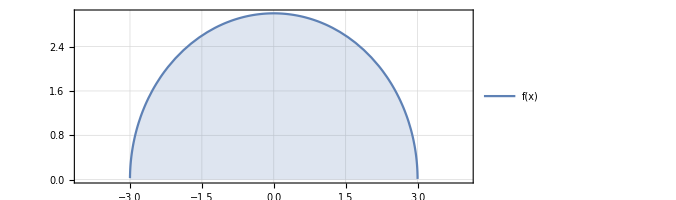

```mathematica
f[x_]:=√(9-x^2)
Plot[f[x],{x,-4,4}, Filling->Bottom,AspectRatio->Automatic,PlotTheme->"Detailed"]
```

```mathematica
Print["Total Charge :"];σ[x_,y_] := √(x^2+ y^2)
∫_-3^3 ∫_0^f[x] σ[x,y]ⅆyⅆx
```

Total Charge :

9 π

#### OR :

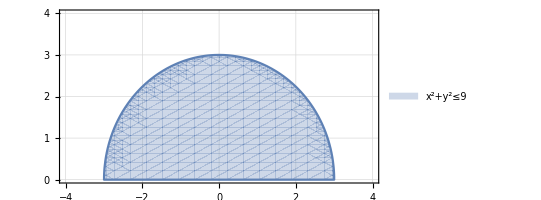

Total Charge :

9 π

```mathematica
RegionPlot[x^2+y^2<=9,{x,-4,4},{y,0,4},AspectRatio->1/2,PlotTheme->"Detailed"]
Print["Total Charge :"];∫_0^Pi ∫_0^3 r*rⅆrⅆt
```

```mathematica
Answer to the question no - 5
(b)
```

```mathematica
ContourPlot3D[{x==0, z ==0, x==5, z-y==0,z==-2y+6}, {x,-6, 6}, {y, -6, 6}, {z, -6,6}, Axes->True , PlotLegends->"Expressions", AxesLabel->Automatic, PlotTheme->"Detailed"]
Print["Volume :  ",∫_0^5 ∫_0^2 ∫_0^y ⅆzⅆyⅆx + ∫_0^5 ∫_2^3 ∫_0^(-2y+6) ⅆzⅆyⅆx]
```

-Graphics3D-

Volume :  15

```mathematica
Answer to the question no - 5
(c)
```

```mathematica
ContourPlot3D[{z==4(x^2+y^2),z==16-4(x^2+y^2)},{x,-1,1},{y,-1,1},{z,0,18}]
Print["Volume : ",∫_-1^1 ∫_-1^1 ∫_(4(x^2+y^2))^(16-4(x^2+y^2)) 1ⅆzⅆxⅆy]
```

-Graphics3D-

Volume : 128/3

```mathematica
Answer to the question no - 6
(a)
```

```mathematica
T[x_,y_] := 10 - 8 x^2-2 y^2
Print["Average Temperature :  ",(∫_0^2 ∫_0^1 T[x,y]ⅆxⅆy)/(∫_0^2 ∫_0^1 ⅆxⅆy)]
```

Average Temperature :  14/3

```mathematica
Answer to the question no - 6
(b)
```

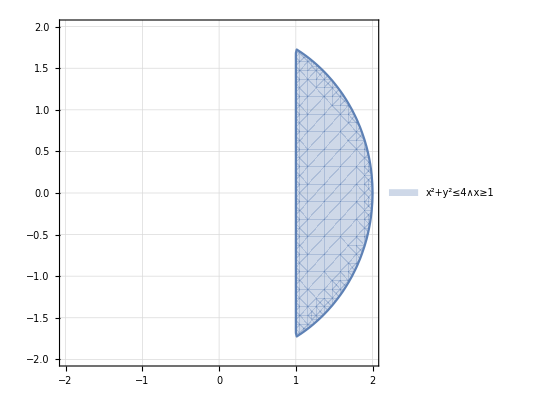

Area :  1/3 (-3 √3+4 π)

```mathematica
RegionPlot[{x^2+y^2≤4&&x≥1},{x,-2,2},{y,-2,2},PlotTheme->"Detailed"]
 Print["Area :  ", 2∫_1^2 √(4-x^2)ⅆx]
```

```mathematica
Answer to the question no - 6
(c)
```

```mathematica
Print["Volume :  ",∫_0^(2π) ∫_(2 Cos[θ])^2 ∫_(-√(4-r^2))^(√(4-r^2)) rⅆzⅆrⅆθ]
ContourPlot3D[{x^2+y^2+z^2==4, x^2+y^2==2x}, {x, -3,3}, {y, -3, 3}, {z, -3,3}, Axes->True, AxesLabel->Automatic, PlotLegends->"Expressions"]
RegionPlot3D[x^2+y^2+z^2<= 4&& x^2+y^2- 2x>=  0,{x,-3,3}, {y, -3,3}, {z, -3, 3}, Axes->True, AxesLabel->Automatic, PlotLegends->"Expressions", MeshStyle->None, ColorFunction->Hue, PlotPoints->50]
```

Volume :  128/9

-Graphics3D-

-Graphics3D-

```mathematica
Answer to the question no - 6
(d)
```

```mathematica
R = 13;
k = 1.5;
DD[r_] = k E^-r;
∫_0^(2π) ∫_0^R DD[r]rⅆrⅆθ
```

9.42448

```mathematica
Answer to the question no - 7
(a)
```

```mathematica
Print["Volume :  ",∫_-3^3 ∫_(-√(9-x^2))^(√(9-x^2)) ∫_1^(5-x) ⅆzⅆyⅆx]
ContourPlot3D[{x^2+y^2==9, z==1, z+x==5}, {x, -3,3}, {y, -3, 3}, {z, 0,3}, Axes->True, AxesLabel->Automatic, PlotLegends->"Expressions"]
RegionPlot3D[x^2+y^2≤ 9&& z≥ 1 && z+x≤ 1,{x,-4,4}, {y, -4,4}, {z, 0, 6}, Axes->True, AxesLabel->Automatic, PlotLegends->"Expressions", MeshStyle->None, ColorFunction->"Rainbow", PlotPoints->50]
```

Volume :  36 π

-Graphics3D-

-Graphics3D-

```mathematica
Answer to the question no - 7
(b)
```

```mathematica
σ[x_,y_]:=1+x^2+y^2
Print["Volume :  ",∫_0^1 ∫_0^(1-x) ∫_(1-x-y)^(1+x+y) σ[x,y]ⅆzⅆyⅆx]
ContourPlot3D[{z==1+x+y, z==1-x-y,x ==0, y==0, y ==1-x}, {x, -10,10}, {y, -10, 10}, {z, -10,10}, Axes->True, AxesLabel->Automatic, PlotLegends->"Expressions"]
```

Volume :  14/15

-Graphics3D-

```mathematica
Answer to the question no - 7
(c)
```

```mathematica
Print["Volume :  ",∫_0^2 ∫_(x^2)^(2x) ∫_0^(x^3+4y) ⅆzⅆyⅆx]
ContourPlot3D[{y == 2x,y == x^2, z ==  0 ,z == x^3+4y}, {x, -5,5}, {y, -5, 5}, {z, 0,30}, Axes->True, AxesLabel->Automatic, PlotLegends->"Expressions"]
RegionPlot3D[y≤  2x && y≥   x^2&& z≥ 0 && z≤   x^3+4y,{x,0,2}, {y, 0,2}, {z, 0, 30}, Mesh->None, PlotPoints->100, Axes->True, AxesLabel->Automatic, PlotTheme->"Detailed", ColorFunction->"Rainbow"]
```

Volume :  32/3

-Graphics3D-

-Graphics3D-

```mathematica
Answer to the question no - 7
(d)
```

```mathematica
P[x_,y_] := E^y;
Q[x_,y_] := x E^y;
If[D[P[x,y],y]==D[Q[x,y], x], Print["Force field is Conservative"], Print["Force field is not conservative"]]
phi[x_,y_]=x E^y+K;
Print["workdone :  " , phi[1,0]-phi[-1,0]]
```

Force field is Conservative

workdone :  2